# Practica 3: Ecuaciones en diferencia

## Ecuaciones en diferencia de primer orden

Resolver y construir el diagrama de fases de las siguientes ecuaciones en diferencia de primer orden.

1. x_t=1/2 x_(t-1)+3          x_0=10

```mathematica
eq1=RSolve[{x[t]==(1/2) x[t-1]+3,x[0]==10},x[t],t]
```

{{x[t]→2^(1-t) (2+3 2^t)}}

```mathematica
Expand[%]
```

{{x[t]→6+2^(2-t)}}

```mathematica
eq1list=Table[{t,N[eq1[[1,1,2]]]},{t,0,25}];
```

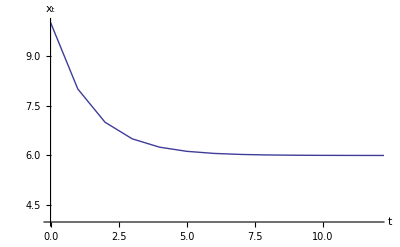

```mathematica
ListPlot[eq1list,Joined->True,PlotRange->{{0,12},{4,10}},AxesLabel->{"t","x_t"}]
```

```mathematica
datos1=TableForm[Table[{t,eq1list},{t,1}]]
```

1 | 0 | 10.
1 | 8.
2 | 7.
3 | 6.5
4 | 6.25
5 | 6.125
6 | 6.0625
7 | 6.03125
8 | 6.01563
9 | 6.00781
10 | 6.00391
11 | 6.00195
12 | 6.00098
13 | 6.00049
14 | 6.00024
15 | 6.00012
16 | 6.00006
17 | 6.00003
18 | 6.00002
19 | 6.00001
20 | 6.
21 | 6.
22 | 6.
23 | 6.
24 | 6.
25 | 6.

```mathematica
f[x_]=3+(1/2)x;
```

```mathematica
Solve[f[x]==x,x]
```

{{x→6}}

```mathematica
puntos1=Rest[Partition[Flatten[Transpose[{NestList[f,10,10],NestList[f,10,10]}]],2,1]];
```

```mathematica
web1=ListPlot[puntos1,Joined->True,PlotRange->{{0,10},{0,10}}];
```

```mathematica
lines1=Plot[{f[x],x},{x,0,10},PlotRange->{0,10}];
```

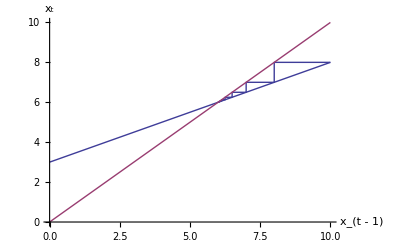

```mathematica
cobweb1=Show[web1,lines1,AxesLabel->{"x_(t - 1)","x_t"}]
```

```mathematica
Clear[eq1,eq1list,datos1,f,puntos1,web1,lines1,cobweb1]
```

2.  x_t=-1/2 x_(t-1)+6          x_0=10

```mathematica
eq2=RSolve[{x[t]==6-(1/2)x[t-1],x[0]==10},x[t],t]
```

{{x[t]→2^(1-t) (3 (-1)^t+2^(1+t))}}

```mathematica
Expand[%]
```

{{x[t]→4+3 (-1)^t 2^(1-t)}}

```mathematica
eq2list=Table[{t,N[eq2[[1,1,2]]]},{t,0,25}];
```

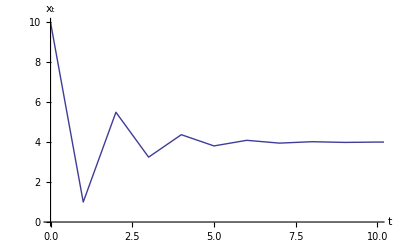

```mathematica
ListPlot[eq2list,Joined->True,PlotRange->{{0,10},{0,10}},AxesLabel->{"t","x_t"}]
```

```mathematica
datos2=TableForm[Table[{t,eq2list},{t,1}]]
```

1 | 0 | 10.
1 | 1.
2 | 5.5
3 | 3.25
4 | 4.375
5 | 3.8125
6 | 4.09375
7 | 3.95313
8 | 4.02344
9 | 3.98828
10 | 4.00586
11 | 3.99707
12 | 4.00146
13 | 3.99927
14 | 4.00037
15 | 3.99982
16 | 4.00009
17 | 3.99995
18 | 4.00002
19 | 3.99999
20 | 4.00001
21 | 4.
22 | 4.
23 | 4.
24 | 4.
25 | 4.

```mathematica
f[x_]=6-(1/2)x;
```

```mathematica
Solve[f[x]==x,x]
```

{{x→4}}

```mathematica
puntos2=Rest[Partition[Flatten[Transpose[{NestList[f,10,10],NestList[f,10,10]}]],2,1]];
```

```mathematica
web2=ListPlot[puntos2,Joined->True,PlotRange->{{0,10},{0,8}}];
```

```mathematica
lines2=Plot[{f[x],x},{x,0,10},PlotRange->{0,10}];
```

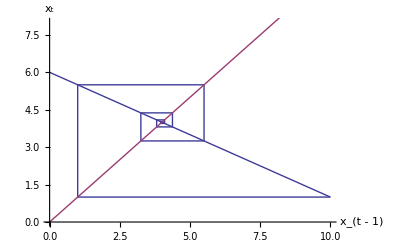

```mathematica
cobweb2=Show[web2,lines2,AxesLabel->{"x_(t - 1)","x_t"}]
```

```mathematica
Clear[eq2,eq2list,datos2,f,puntos2,web2,lines2,cobweb2]
```

3. x_t=2 x_(t-1)-2          x_0=3

```mathematica
eq3=RSolve[{x[t]==-2+2x[t-1],x[0]==3},x[t],t]
```

{{x[t]→2+2^t}}

```mathematica
eq3list=Table[{t,N[eq3[[1,1,2]]]},{t,0,10}];
```

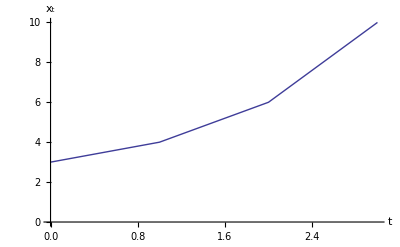

```mathematica
ListPlot[eq3list,Joined->True,PlotRange->{{0,3},{0,10}},AxesLabel->{"t","x_t"}]
```

```mathematica
datos3=TableForm[Table[{t,eq3list},{t,1}]]
```

1 | 0 | 3.
1 | 4.
2 | 6.
3 | 10.
4 | 18.
5 | 34.
6 | 66.
7 | 130.
8 | 258.
9 | 514.
10 | 1026.

```mathematica
f[x_]=-2+2x;
```

```mathematica
Solve[f[x]==x,x]
```

{{x→2}}

```mathematica
puntos3=Rest[Partition[Flatten[Transpose[{NestList[f,3,5],NestList[f,3,5]}]],2,1]];
```

```mathematica
web3=ListPlot[puntos3,Joined->True,PlotRange->{{0,10},{0,10}}];
```

```mathematica
lines3=Plot[{f[x],x},{x,0,10},PlotRange->{0,10}];
```

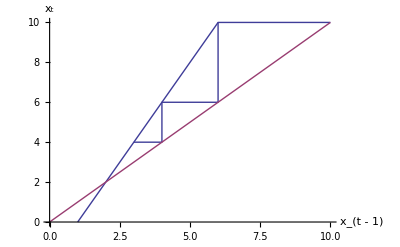

```mathematica
cobweb3=Show[web3,lines3,AxesLabel->{"x_(t - 1)","x_t"}]
```

```mathematica
Clear[eq3,eq3list,datos3,f,puntos3,web3,lines3,cobweb3]
```

4. x_t=-2 x_(t-1)+3          x_0=2

```mathematica
eq4=RSolve[{x[t]==3-2x[t-1],x[0]==2},x[t],t]
```

{{x[t]→1-(-2)^t+(-1)^t 2^(1+t)}}

```mathematica
Expand[%]
```

{{x[t]→1-(-2)^t+(-1)^t 2^(1+t)}}

```mathematica
eq4list=Table[{t,N[eq4[[1,1,2]]]},{t,0,10}];
```

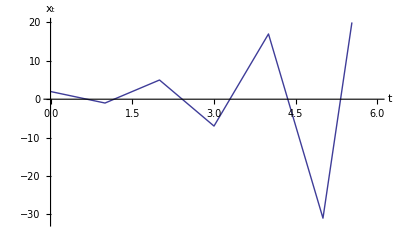

```mathematica
ListPlot[eq4list,Joined->True,PlotRange->{{0,6},{-32,20}},AxesLabel->{"t","x_t"}]
```

```mathematica
datos4=TableForm[Table[{t,eq4list},{t,1}]]
```

1 | 0 | 2.
1 | -1.
2 | 5.
3 | -7.
4 | 17.
5 | -31.
6 | 65.
7 | -127.
8 | 257.
9 | -511.
10 | 1025.

```mathematica
f[x_]=3-2x;
```

```mathematica
Solve[f[x]==x,x]
```

{{x→1}}

```mathematica
puntos4=Rest[Partition[Flatten[Transpose[{NestList[f,2,10],NestList[f,2,10]}]],2,1]];
```

```mathematica
web4=ListPlot[puntos4,Joined->True,PlotRange->{{-10,20},{-10,20}}];
```

```mathematica
lines4=Plot[{f[x],x},{x,-10,20},PlotRange->{-10,20}];
```

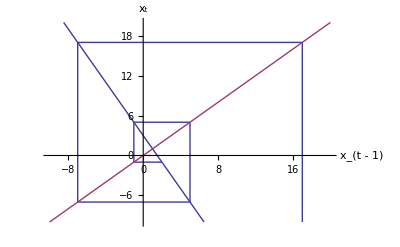

```mathematica
cobweb4=Show[web4,lines4,AxesLabel->{"x_(t - 1)","x_t"}]
```

```mathematica
Clear[eq4,eq4list,datos4,f,puntos4,web4,lines4,cobweb4]
```

## Ecuaciones en diferencia de segundo orden

Resuelver analiticamente las siguientes ecuaciones en diferencia de segundo orden.

1. x_(t+2)-3 x_(t+1)+2 x_t=0

```mathematica
eq1=RSolve[{x[t+2]-3x[t+1]+2x[t]==0},x[t],t]
```

{{x[t]→C[1]+2^t C[2]}}

2. x_(t+2)+x_t=0

```mathematica
eq2=RSolve[{x[t+2]+x[t]==0},x[t],t]
```

{{x[t]→ⅈ^t C[1]+(-ⅈ)^t C[2]}}

3. x_(t+2)+6 x_(t+1)+9 x_t=0

```mathematica
eq3=RSolve[{x[t+2]+6x[t+1]+9x[t]==0},x[t],t]
```

{{x[t]→(-3)^t C[1]+(-3)^t t C[2]}}

4. x_(t+2)+x_(t+1)-6 x_t=0               x_0=1   x_1=2

```mathematica
eq4=RSolve[{x[t+2]+x[t+1]-6x[t]==0,x[0]==1,x[1]==2},x[t],t]
```

{{x[t]→2^t}}

5. x_(t+2)+8 x_(t+1)+16 x_t=0               x_0=0   x_1=4

```mathematica
eq5=RSolve[{x[t+2]+8x[t+1]+16x[t]==0,x[0]==0,x[1]==4},x[t],t]
```

{{x[t]→-(-4)^t t}}

6. x_(t+2)-8 x_(t+1)-9 x_t=24               x_0=2   x_1=0

```mathematica
eq6=RSolve[{x[t+2]-8x[t+1]-9x[t]==24,x[0]==2,x[1]==0},x[t],t]
```

{{x[t]→1/2 (-3+6 (-1)^t+9^t)}}

```mathematica
Expand[%]
```

{{x[t]→-3/2+3 (-1)^t+9^t/2}}

7.  3 x_(t+2)-10 x_(t+1)+3 x_t=8               x_0=5   x_1=3

```mathematica
eq7=RSolve[{3x[t+2]-10x[t+1]+3x[t]==8,x[0]==5,x[1]==3},x[t],t]
```

{{x[t]→3^-t (6-2 3^t+3^(2 t))}}

```mathematica
Expand[%]
```

{{x[t]→-2+2 3^(1-t)+3^t}}

## Sistema de ecuaciones en diferencia

Resuelva graficamente los siguientes sistemas de ecuaciones en diferencia.

1. x_t=0.25 x_(t-1)+0.4 y_(t-1)-5          x_0=10
    y_t=      -x_(t-1)+        y_(t-1)+10       y_0=  5

```mathematica
Clear[x,y,t]
```

```mathematica
x[0]:=10; y[0]=5;
```

```mathematica
x[t_]:=x[t]=0.25x[t-1]+0.4y[t-1]-5
```

```mathematica
y[t_]:=y[t]=-x[t-1]+y[t-1]+10
```

```mathematica
data:=Table[{x[t],y[t]},{t,0,20}];
```

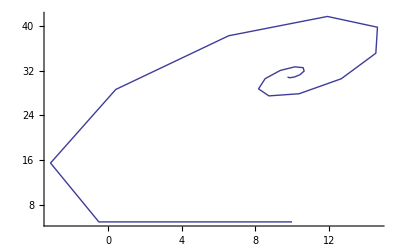

```mathematica
ListPlot[data,Joined->True,PlotRange->All]
```

```mathematica
Clear[x,y,t]
```

2. x_t=0.5 x_(t-1)+0.3 y_(t-1)+  8        x_0=25
    y_t=    -x_(t-1)+       y_(t-1)+30       y_0=10

```mathematica
x[0]:=25; y[0]=10;
```

```mathematica
x[t_]:=x[t]=0.5x[t-1]+0.3y[t-1]+8
```

```mathematica
y[t_]:=y[t]=-x[t-1]+y[t-1]+30
```

```mathematica
data:=Table[{x[t],y[t]},{t,0,40}];
```

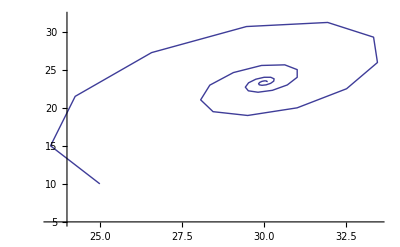

```mathematica
ListPlot[data,Joined->True,PlotRange->{5,32}]
```

```mathematica
Clear[x,y,t]
```

3. x_t=2 x_(t-1)-2 y_(t-1)+5          x_0=1
    y_t=    x_(t-1)-   y_(t-1)+4          y_0=2

```mathematica
x[0]:=1; y[0]=2;
```

```mathematica
x[t_]:=x[t]=2x[t-1]-2y[t-1]+5
```

```mathematica
y[t_]:=y[t]=x[t-1]-y[t-1]+4
```

```mathematica
data:=Table[{x[t],y[t]},{t,0,2}];
```

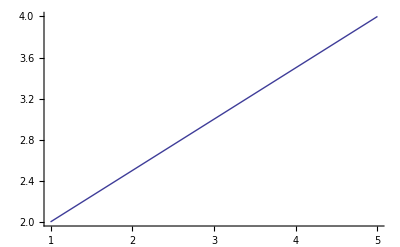

```mathematica
ListPlot[data,Joined->True,PlotRange->All]
```

```mathematica
Clear[x,y,t]
```

## Ecuaciones en diferencia aplicadas a la economía

Considere el siguiente ejemplo numérico.

Dinámica del mercado de bienes en tiempo discreto
		C_t=a+bY_t
		E_t=C_t+I+G
		ΔY_(t+1)=λ(E_t-Y_t)

```mathematica
Clear[a,b,i,g,λ]
```

```mathematica
{a=110,b=0.75,i=200,g=100,λ=1};
```

```mathematica
eq1=RSolve[{y[t+1]==(λ (a+i+g))+(1-λ (1-b))y[t],y[0]==1000},y[t],t]
```

{{y[t]→1.33333^(-1. t) 2.^(-2. t) (1000. 2.^(2. t)+1640. 1.33333^(1. t) 2.^(2. t)-1640. 1.33333^(1. t) 3.^t)}}

```mathematica
Simplify[%]
```

{{y[t]→1640.-640. ⅇ^(-0.287682 t)}}

```mathematica
eq2=RSolve[{y[t+1]==(2 (a+i+g))+(1-2(1-b))y[t],y[0]==1000},y[t],t]
```

{{y[t]→2.^(-1. t) (-640.+1640. 2.^t)}}

```mathematica
Simplify[%]
```

{{y[t]→1640.-640. ⅇ^(-0.693147 t)}}

```mathematica
eq1list=Table[{t,N[eq1[[1,1,2]]]},{t,0,45}];
```

```mathematica
eq2list=Table[{t,N[eq2[[1,1,2]]]},{t,0,45}];
```

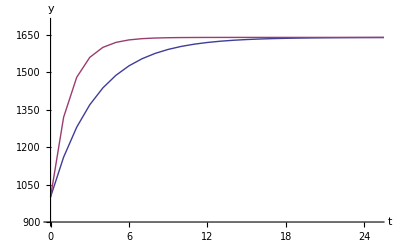

```mathematica
ListPlot[{eq1list,eq2list},PlotJoined->True,AxesLabel->{"t","y"},PlotRange->{{0,25},{900,1700}}]
```

```mathematica
datos1=TableForm[Table[{t,eq1list,eq2list},{t,1}]]
```

1 | 0 | 1000.
1 | 1160.
2 | 1280.
3 | 1370.
4 | 1437.5
5 | 1488.13
6 | 1526.09
7 | 1554.57
8 | 1575.93
9 | 1591.95
10 | 1603.96
11 | 1612.97
12 | 1619.73
13 | 1624.8
14 | 1628.6
15 | 1631.45
16 | 1633.59
17 | 1635.19
18 | 1636.39
19 | 1637.29
20 | 1637.97
21 | 1638.48
22 | 1638.86
23 | 1639.14
24 | 1639.36
25 | 1639.52
26 | 1639.64
27 | 1639.73
28 | 1639.8
29 | 1639.85
30 | 1639.89
31 | 1639.91
32 | 1639.94
33 | 1639.95
34 | 1639.96
35 | 1639.97
36 | 1639.98
37 | 1639.98
38 | 1639.99
39 | 1639.99
40 | 1639.99
41 | 1640.
42 | 1640.
43 | 1640.
44 | 1640.
45 | 1640. | 0 | 1000.
1 | 1320.
2 | 1480.
3 | 1560.
4 | 1600.
5 | 1620.
6 | 1630.
7 | 1635.
8 | 1637.5
9 | 1638.75
10 | 1639.38
11 | 1639.69
12 | 1639.84
13 | 1639.92
14 | 1639.96
15 | 1639.98
16 | 1639.99
17 | 1640.
18 | 1640.
19 | 1640.
20 | 1640.
21 | 1640.
22 | 1640.
23 | 1640.
24 | 1640.
25 | 1640.
26 | 1640.
27 | 1640.
28 | 1640.
29 | 1640.
30 | 1640.
31 | 1640.
32 | 1640.
33 | 1640.
34 | 1640.
35 | 1640.
36 | 1640.
37 | 1640.
38 | 1640.
39 | 1640.
40 | 1640.
41 | 1640.
42 | 1640.
43 | 1640.
44 | 1640.
45 | 1640.

```mathematica
f[y_]=(λ*(a+i+g))+(1-λ*(1-b))y
```

410+0.75 y

```mathematica
Solve[f[y]==y,y]
```

{{y→1640.}}

```mathematica
puntos1=Rest[Partition[Flatten[Transpose[{NestList[f,1000,10],NestList[f,1000,10]}]],2,1]];
```

```mathematica
web1=ListPlot[puntos1,PlotJoined->True,PlotRange->{{900,1680},{900,1680}}];
```

```mathematica
lines1=Plot[{f[y],y},{y,900,1680},PlotRange->{900,1680}];
```

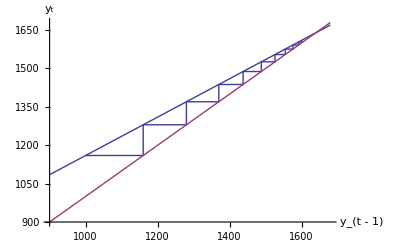

```mathematica
cobweb1=Show[web1,lines1,AxesLabel->{"y_(t - 1)","y_t"}]
```

```mathematica
Clear[eq1,eq1list,datos1,f,puntos1,web1,lines1,cobweb1]
```